```mathematica
PointGenerator[num_, polygon_]:=Block[{
P = List[],Pvector=List[],
PI,PIvector,
i,t,
minX= Infinity,minY=Infinity,
maxX = -1, maxY =-1,
length,
result
},
length = Length[polygon];

For[i = 1, i ≤ length,++i,
If[Part[Part[polygon,i],1]<minX,minX =Part[Part[polygon,i],1]];
If[Part[Part[polygon,i],2]<minY,minY =Part[Part[polygon,i],2]];

If[Part[Part[polygon,i],1]>maxX,maxX =Part[Part[polygon,i],1]];
If[Part[Part[polygon,i],2]> maxY,maxY =Part[Part[polygon,i],2]];
];
For[ t = 0, t< num, t++;,
	PI={RandomInteger[{minX, maxX}], RandomInteger[{minY, maxY}]}; 
	 PIvector = {RandomInteger[{-50, 50}], RandomInteger[{-50, 50}]}; 
	AppendTo[Pvector,PIvector];
	AppendTo[P,PI];
];
result ={P,Pvector};
Return[result];];
```

```mathematica
PoligonPreCount[SPolygon_] :=Block[{
P = List[], 
S =List[], 
result,n,
smallPolygonLength
},
smallPolygonLength = Length[SPolygon];
For[n = 1, n <smallPolygonLength , ++n,
AppendTo[P,Part[SPolygon, n+1]-Part[SPolygon, n]];
];
Return [P]];
```

```mathematica
PolygonSizes [polygon_]:= Block[{
minX= Infinity,minY=Infinity,
maxX = -1, maxY =-1,
length,
result
},
length = Length[polygon];

For[i = 1, i ≤ length,++i,
If[Part[Part[polygon,i],1]<minX,minX =Part[Part[polygon,i],1]];
If[Part[Part[polygon,i],2]<minY,minY =Part[Part[polygon,i],2]];

If[Part[Part[polygon,i],1]>maxX,maxX =Part[Part[polygon,i],1]];
If[Part[Part[polygon,i],2]> maxY,maxY =Part[Part[polygon,i],2]];
];
result = {{minX,minY},{maxX, maxY}};
Return[result]
]
```

```mathematica
Test[point_, PSize_] := Block[{
flag = True,
X,Y,
minX,minY,
maxX, maxY,
},
X= Part[point,1];
Y = Part[point, 2];

minX = Part[Part[PSize, 1],1]; minY = Part[Part[PSize, 1],2];
maxX = Part[Part[PSize, 2],1]; maxY = Part[Part[PSize, 2],2];
If[(maxX > X > minX)&&(maxY> Y > minY),,flag = False];
Return[flag]]
```

```mathematica
move[Bpolygon_,SPPC_, PSize_] := Block[{
P=List[],
PI,P1,
VI,V1,
b,a,
i,n,n2,
length,
polygonLength,
flag =1,
result,
usePoints,useVectors,polygonID
},
For[polygonID = 1, polygonID ≤  Length[points],polygonID++,

usePoints = points[[polygonID]];
useVectors = vectors[[polygonID]];
length = Length[usePoints];
polygonLength = Length[Bpolygon];
For[i = 1, i <= length,i++,
If[Part[useVectors, i] == {0,0},Print[Part[usePoints,i], i],

PI=Part[usePoints,i]+(Part[useVectors,i]);
P1 = Part[usePoints,i];


If[Test[PI,PSize],
Part[usePoints,i] = PI;,
For[n = 1, n <polygonLength &&  flag == 1, ++n,
If[((Det[{Part[SPPC, n],PI-Part[Bpolygon,n]}]*Det[{Part[SPPC, n],P1-Part[Bpolygon,n]}] > 0)||
		 (Det[{PI-P1,Part[Bpolygon,n]-P1}]*Det[{PI-P1,Part[Bpolygon,n+1]-P1}]>0 ))
			,
, 
b=Part[Bpolygon, n+1]-Part[Bpolygon, n];
a =Part[useVectors,i];
VI = 2((a.b)/(b.b))*b - a;
Part[vectors[[polygonID]],i] = VI;
flag =0];
];
If[flag == 1, 
Print["хм..."]];


];
];
];
(*result = NearestPair[usePoints];
minLine = result[[1]];
If[result[[2]] < 200,textField = "Бадабум!!!", textField = " "];
*)
polygon[[polygonID]] = PolygonBilder[usePoints];
points[[polygonID]] = usePoints;

 ];
(*Print[polygon[[1]]];
Print[polygon[[2]]];*)
intersection = PolygonIntersection[polygon[[1]],polygon[[2]]];
Return[]];
```

```mathematica
(*Алгаритм Грэхама*)
PolygonBilder[points_]:=Block[{
P = List[],
Pl = List[],Pr = List[],
Sl = List[], Sr= List[],
PlPoint , PrPoint,
length,n,
result
},
length = Length[points];
PlPoint = Part[points,1];
PrPoint =Part[points,1];

(*находим минимумальную и максимальную по иксам точку*)
For[n = 2, n ≤  length,++n,

If[Part[Part[points,n],1]<Part[PlPoint,1],PlPoint =Part[points,n]];
If[Part[Part[points,n],1]>Part[PrPoint,1],PrPoint =Part[points,n]];
];

(*делим множество на два подмножества*)
For[n = 1, n ≤  length,++n,
If[Part[points, n]== PlPoint ||Part[points, n]== PrPoint,,
If[Det[{PrPoint-PlPoint,Part[points, n]-PlPoint }]<0,AppendTo[Pr,Part[points, n]], AppendTo[Pl,Part[points, n]]]
];
];

(*вернем точки а то не хо*)
AppendTo[Pr, PlPoint];
AppendTo[Pl, PrPoint];


(*упорядочиваем*)
Pr = SortBy[Pr, First];
Pl= SortBy[Pl, First];
(*построение выпуклой оболочки для множества Pl*)
length = Length[Pl];
AppendTo[Sl, PlPoint];
For[n = 1, n ≤  length,++n,
If[Length[Sl]== 1,AppendTo[Sl,Part[Pl,n]],
If[Det[{Part[Sl, Length[Sl]]-Part[Sl, Length[Sl]-1],Part[Pl, n]-Part[Sl, Length[Sl]-1] }]≤ 0,
 AppendTo[Sl,Part[Pl,n]];,
 Sl = Delete[Sl, Length[Sl]]; n--;
];
];
];
(*построение выпуклой оболочки для множества Pr*)
length = Length[Pr];
AppendTo[Sr, PrPoint];
For[n = length,   1≤ n,--n,
If[Length[Sr]== 1,AppendTo[Sr,Part[Pr,n]],
If[Det[{Part[Sr, Length[Sr]]-Part[Sr, Length[Sr]-1],Part[Pr, n]-Part[Sr, Length[Sr]-1] }]< 0,
 AppendTo[Sr,Part[Pr,n]];,
 Sr = Delete[Sr, Length[Sr]]; n++;
];
];
];


Sr = Delete[Sr, 1];
result = Join[Sl,Sr];


Return[result]]
```

```mathematica
SegmentIntersect[p_,q_]:= Block[{flag},
flag = !((Det[{p[[2]]-p[[1]],q[[2]]-p[[1]]}]*Det[{p[[2]]-p[[1]],q[[1]]-p[[1]]}])>0||
(Det[{q[[2]]-q[[1]],p[[2]]-q[[1]]}]*Det[{q[[2]]-q[[1]],p[[1]]-q[[1]]}])>0);
Return[flag]
]
```

```mathematica
PointRightForLine[p_,line_]:= Block[{flag},
flag = (Det[{line[[2]]- line[[1]],p-line[[1]]}] <0);
Return[flag]]
```

{{3998683409/2032103,2014384883/4064206},{2040028277/509259,489664854/169753},{4093,3028},{3577,3474},{2219591549/1435197,6208088063/1435197},{521539126/567893,1044139587/567893},{3998683409/2032103,2014384883/4064206}}

{{1967.76,495.64},{4005.88,2884.57},{4093.,3028.},{3577.,3474.},{1546.54,4325.6},{918.376,1838.62},{1967.76,495.64}}

{{481,107},{1655,4755},{2527,4942},{4943,3983},{1951,476},{1399,258},{481,107}}

{{414,3102},{785,4645},{3577,3474},{4093,3028},{2298,73},{636,2200},{500,2492},{414,3102}}

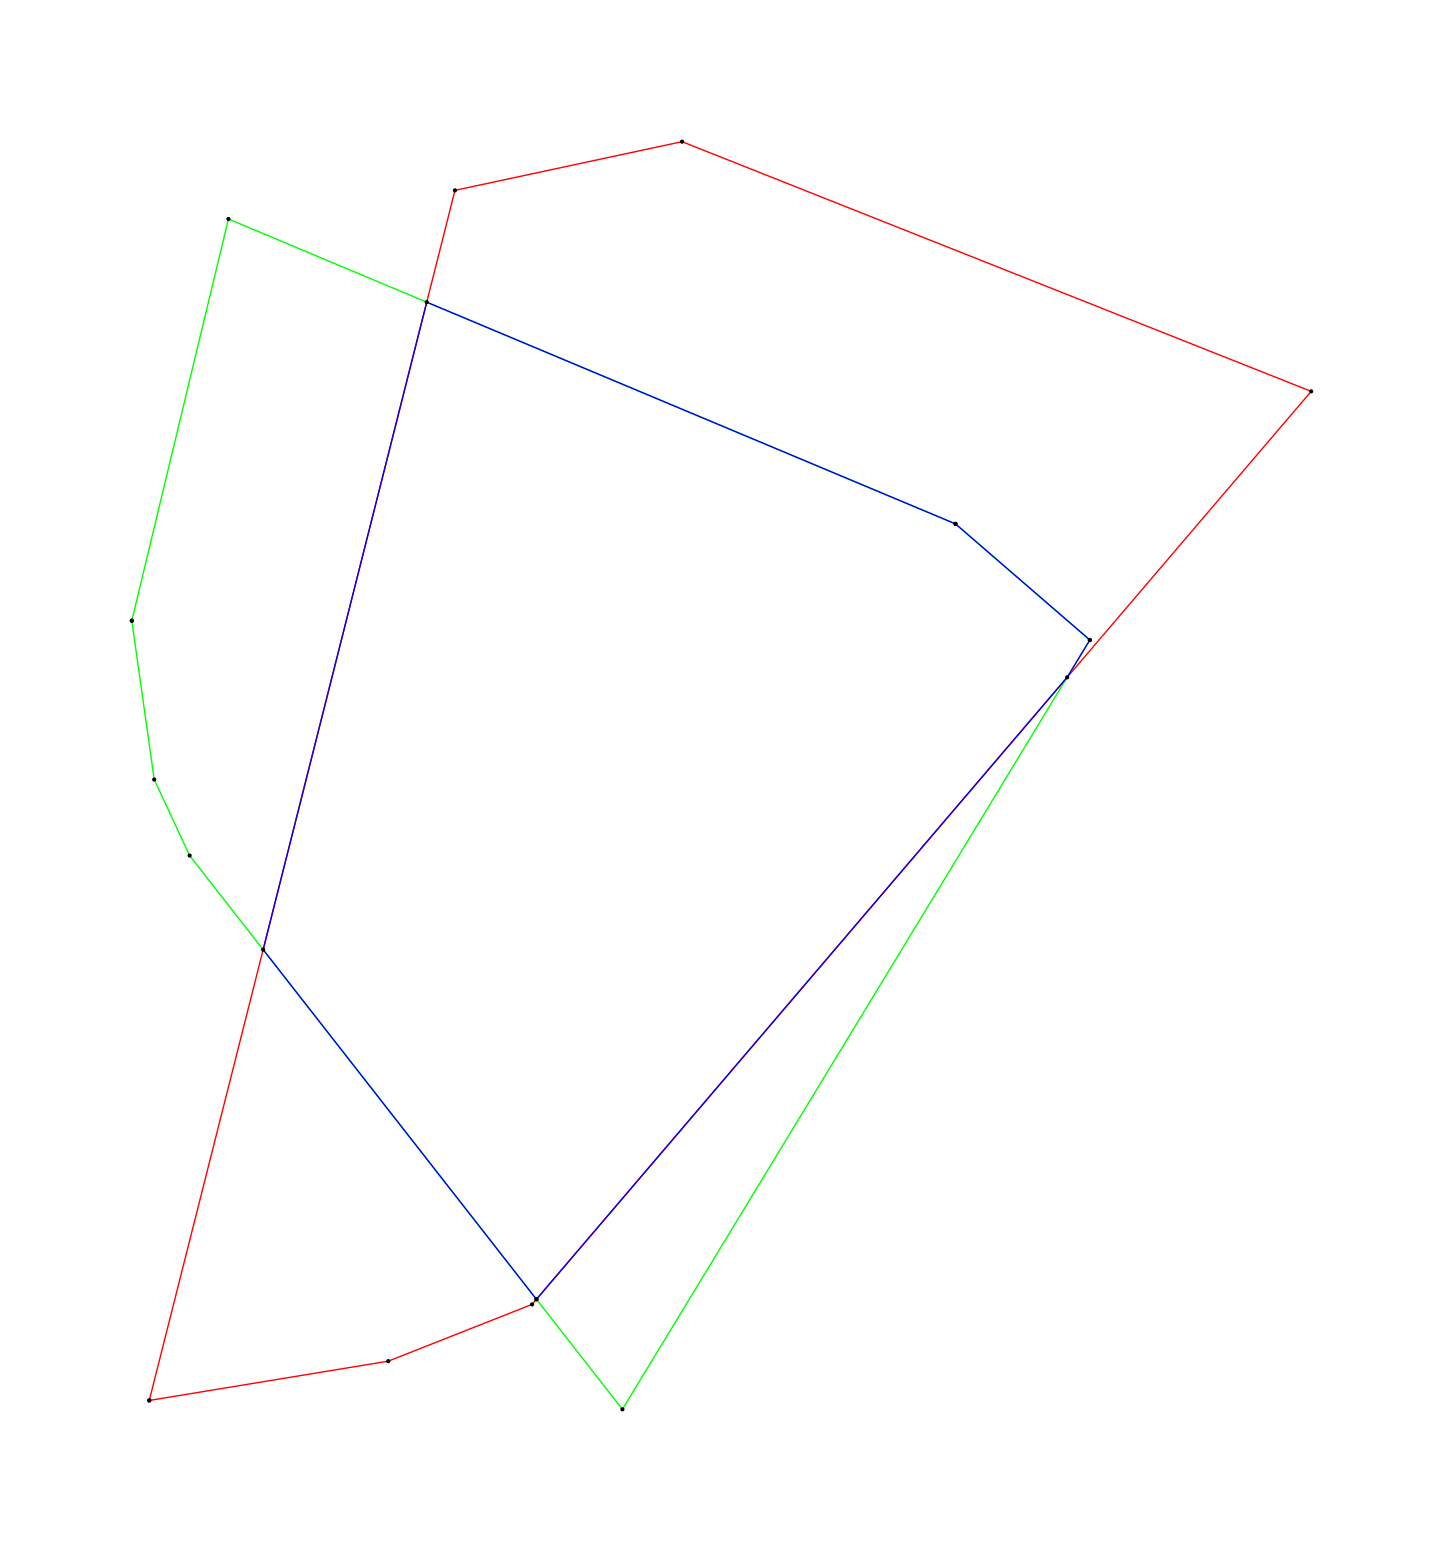

{{1961121118/1008759,112553399/336253},{26651178314/5837989,5057002535/5837989},{606679084/132609,721392919/663045},{4228,2227},{8253076508/3035671,11700625109/3035671},{8267778604/11100251,48195617213/11100251},{1576506548/2659847,5298757921/2659847},{924,403},{1961121118/1008759,112553399/336253}}

{{1944.09,334.728},{4565.13,866.223},{4574.95,1088.},{4228.,2227.},{2718.7,3854.38},{744.828,4341.85},{592.706,1992.13},{924.,403.},{1944.09,334.728}}

{{466,35},{773,4777},{2643,3936},{4228,2227},{4638,881},{466,35}}

{{68,4509},{4676,3371},{4551,547},{4510,163},{924,403},{68,4509}}

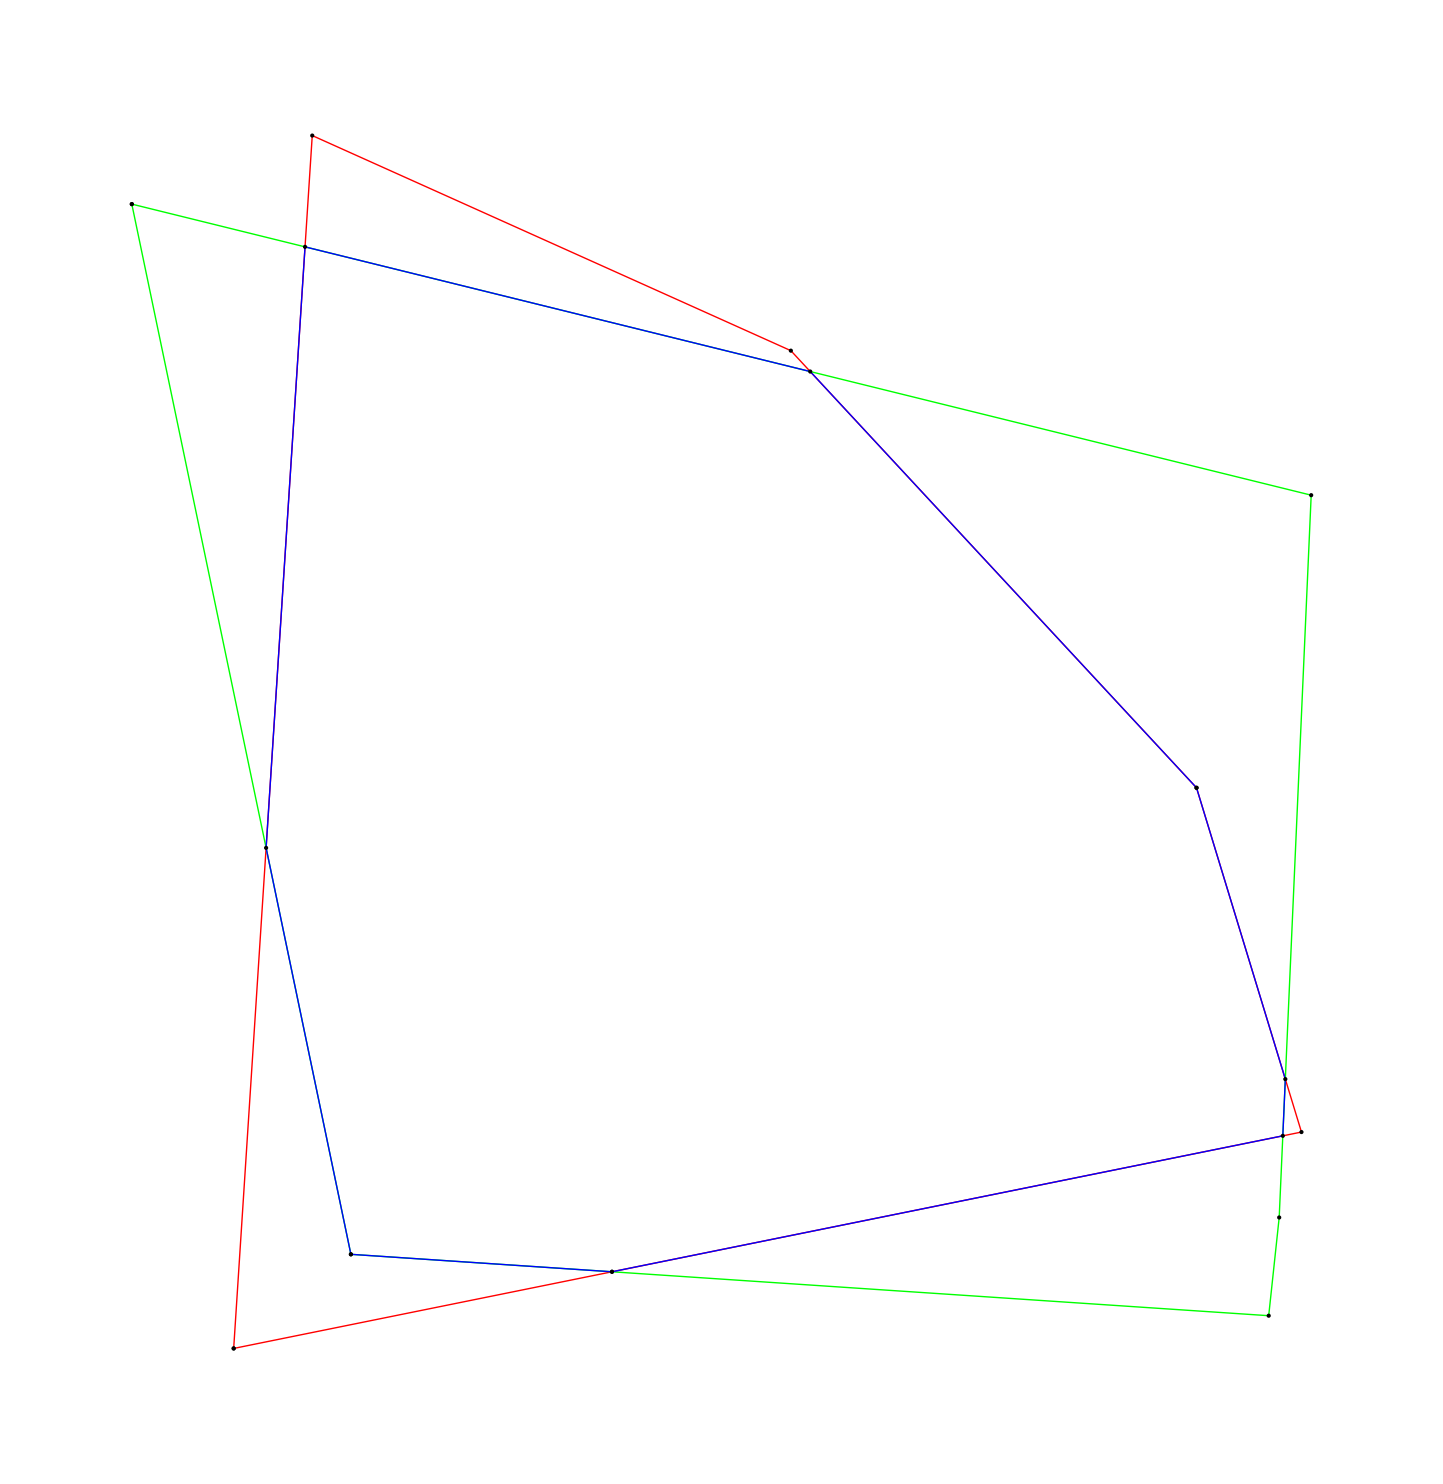

```mathematica
LookOn[b_,a_] := Block[{
det1,det2,
a0,a1,b1,
result = False},
det1 = Det[{a[[2]]-a[[1]],b[[2]]- b[[1]]}];
det2 = Det[{a[[2]]-a[[1]],b[[2]]- a[[1]]}];
If[det1>0 && det2 <0, result = True,
If[det1 <0 && det2>0, result = True];
];
Return[result]]

PolygonIntersection[polygon1_,polygon2_] := Block[{
workPolygon1, workPolygon2,
result = List[],
p,q,
i,n=1,
N,T, R,
flag = False,
Nflag = False,
append={},
t
}, 
workPolygon1 = Reverse[polygon1];
workPolygon1 = Delete[workPolygon1, Length[workPolygon1]];
workPolygon2 = Reverse[polygon2];
workPolygon2 = Delete[workPolygon2, Length[workPolygon2]];

For[i = 1; t=0,(i <   Length[workPolygon1]|| n <  Length[workPolygon2]|| flag)&& t<(Length[workPolygon1]+ Length[workPolygon2])*2,t++,

p = {workPolygon1[[Mod[i,Length[workPolygon1],1]]], workPolygon1[[Mod[i+1,Length[workPolygon1],1]]]};
q = {workPolygon2[[Mod[n,Length[workPolygon2],1]]], workPolygon2[[Mod[n+1,Length[workPolygon2],1]]]};
(*
Print["Loop"];
Print[p];
Print[q];*)
If[LookOn[p,q]&&LookOn[q,p],
If[Det[{p[[2]]- p[[1]],q[[1]]-p[[1]]}] >0,i++ ; (*Print[1];*),n++; (*Print[2];*)];
,
If[LookOn[p,q]&&!LookOn[q,p],
If[PointRightForLine[p[[2]],q]||PointRightForLine[p[[1]],q],i++;  (*Print[4];*),i++;append = p[[2]];  (*Print[3]*);]
,
If[!LookOn[p,q]&&LookOn[q,p],
If[PointRightForLine[q[[2]],p]||PointRightForLine[q[[1]],p],n++;(*  Print[6];*),n++;append = q[[2]];(* Print[5];*)]
,
If[!SegmentIntersect[p,q]
, 

(*Print[8]*)
,

N={-Part[q[[2]],2]+Part[q[[1]],2],Part[q[[2]],1]-Part[q[[1]],1]};
T = ((q[[1]]-p[[1]]).N)/((p[[2]]-p[[1]]).N);
append = p[[1]]*(1-T)+p[[2]]*T;
Nflag = True;
(*Print[7];*)

];
If[Det[{p[[2]]- p[[1]],q[[2]]-p[[1]]}] >0,i++;(*Print["p"]*),n++;(*Print["q"]*)];
];
];
];
If[append ≠  {}&&Nflag,AppendTo[result,append];];
append = {};
If[Length[result]> 0,If[result[[1]] == result[[Length[result]]],flag =False, flag = True]];

(*Print[result];
Print[i," ", n];*)
];
Return[result]]


p1 ={{481,107},{1655,4755},{2527,4942},{4943,3983},{1951,476},{1399,258},{481,107}};
p2 ={{414,3102},{785,4645},{3577,3474},{4093,3028},{2298,73},{636,2200},{500,2492},{414,3102}};


mp = PolygonIntersection[p1,p2]
N[mp]
p1
p2
Graphics[{Red, Line[p1], Green, Line[p2],Blue,Line[mp],Black, Point[Join[p1,p2]],Point[mp]}]

p1 = {{466,35},{773,4777},{2643,3936},{4228,2227},{4638,881},{466,35}};
p2 = {{68,4509},{4676,3371},{4551,547},{4510,163},{924,403},{68,4509}};

mp = PolygonIntersection[p1,p2]
N[mp]
p1
p2
Graphics[{Red, Line[p1], Green, Line[p2],Blue,Line[mp],Black, Point[Join[p1,p2]],Point[mp]}]
```

```mathematica
square = {{0,0},{0,5000},{5000,5000},{5000,0},{0,0}}
pointVector = PointGenerator[10, square];
pointVector2 = PointGenerator[10, square];
points = {Part[pointVector,1],Part[pointVector2,1]};
vectors ={ Part[pointVector, 2], Part[pointVector2, 2]};
BPPC = PoligonPreCount[square];
PSize = PolygonSizes[square];
polygon ={{},{}};
move[square,BPPC,PSize];
intersection
Graphics[{Line[{square}],Yellow, Polygon[Dynamic[polygon[[1]]]],Red, Polygon[Dynamic[polygon[[2]]]] , Blue, Polygon[Dynamic[intersection]]}]
Dynamic[move[square,BPPC,PSize]]
(*Graphics[{Line[{square}],Blue,Point[Dynamic[move[square,BPPC,PSize,1]]],Yellow, Polygon[Dynamic[polygon[[1]]]],Blue,Point[Dynamic[move[square,BPPC,PSize,2]]],Red, Polygon[Dynamic[polygon[[2]]]] }]*)
```

{{0,0},{0,5000},{5000,5000},{5000,0},{0,0}}

{{2618763741/767687,2119125830/767687},{57646107/22063,99500563/22063},{306943491/123899,552532163/123899},{8159348785/5379439,9558260524/5379439},{2668,1459},{3008,1529},{2618763741/767687,2119125830/767687}}

-Graphics-

```mathematica
move[square,BPPC,PSize];
Graphics[{Line[{square}],Green, Polygon[Dynamic[polygon[[1]]]],Red, Polygon[Dynamic[polygon[[2]]]] , Blue, Polygon[Dynamic[intersection]]}]
```

{{481,107},{1655,4755},{2527,4942},{4943,3983},{1951,476},{1399,258},{481,107}}

{{338,2492},{414,3102},{785,4645},{3577,3474},{4093,3028},{2298,73},{536,445},{338,2492}}

Loop

{{481,107},{1399,258}}

{{338,2492},{536,445}}

5

{{536,445}}

Loop

{{481,107},{1399,258}}

{{536,445},{2298,73}}

4

{{536,445}}

Loop

{{1399,258},{1951,476}}

{{536,445},{2298,73}}

7

q

{{536,445},{207330839/147365,38481131/147365}}

Loop

{{1399,258},{1951,476}}

{{2298,73},{4093,3028}}

3

{{536,445},{207330839/147365,38481131/147365},{1951,476}}

Loop

{{1951,476},{4943,3983}}

{{2298,73},{4093,3028}}

7

p

{{536,445},{207330839/147365,38481131/147365},{1951,476},{2040028277/509259,489664854/169753}}

Loop

{{4943,3983},{2527,4942}}

{{2298,73},{4093,3028}}

5

{{536,445},{207330839/147365,38481131/147365},{1951,476},{2040028277/509259,489664854/169753},{4093,3028}}

Loop

{{4943,3983},{2527,4942}}

{{4093,3028},{3577,3474}}

1

{{536,445},{207330839/147365,38481131/147365},{1951,476},{2040028277/509259,489664854/169753},{4093,3028}}

Loop

{{2527,4942},{1655,4755}}

{{4093,3028},{3577,3474}}

5

{{536,445},{207330839/147365,38481131/147365},{1951,476},{2040028277/509259,489664854/169753},{4093,3028},{3577,3474}}

Loop

{{2527,4942},{1655,4755}}

{{3577,3474},{785,4645}}

4

{{536,445},{207330839/147365,38481131/147365},{1951,476},{2040028277/509259,489664854/169753},{4093,3028},{3577,3474}}

Loop

{{1655,4755},{481,107}}

{{3577,3474},{785,4645}}

7

q

{{536,445},{207330839/147365,38481131/147365},{1951,476},{2040028277/509259,489664854/169753},{4093,3028},{3577,3474},{2219591549/1435197,6208088063/1435197}}

Loop

{{1655,4755},{481,107}}

{{785,4645},{414,3102}}

2

{{536,445},{207330839/147365,38481131/147365},{1951,476},{2040028277/509259,489664854/169753},{4093,3028},{3577,3474},{2219591549/1435197,6208088063/1435197}}

Loop

{{1655,4755},{481,107}}

{{414,3102},{338,2492}}

2

{{536,445},{207330839/147365,38481131/147365},{1951,476},{2040028277/509259,489664854/169753},{4093,3028},{3577,3474},{2219591549/1435197,6208088063/1435197}}

Loop

{{1655,4755},{481,107}}

{{338,2492},{536,445}}

6

{{536,445},{207330839/147365,38481131/147365},{1951,476},{2040028277/509259,489664854/169753},{4093,3028},{3577,3474},{2219591549/1435197,6208088063/1435197}}

Loop

{{1655,4755},{481,107}}

{{536,445},{2298,73}}

7

p

{{536,445},{207330839/147365,38481131/147365},{1951,476},{2040028277/509259,489664854/169753},{4093,3028},{3577,3474},{2219591549/1435197,6208088063/1435197},{609068901/1078313,473284787/1078313}}

Loop

{{481,107},{1399,258}}

{{536,445},{2298,73}}

4

{{536,445},{207330839/147365,38481131/147365},{1951,476},{2040028277/509259,489664854/169753},{4093,3028},{3577,3474},{2219591549/1435197,6208088063/1435197},{609068901/1078313,473284787/1078313}}

Loop

{{1399,258},{1951,476}}

{{536,445},{2298,73}}

7

q

{{536,445},{207330839/147365,38481131/147365},{1951,476},{2040028277/509259,489664854/169753},{4093,3028},{3577,3474},{2219591549/1435197,6208088063/1435197},{609068901/1078313,473284787/1078313},{207330839/147365,38481131/147365}}

Loop

{{1399,258},{1951,476}}

{{2298,73},{4093,3028}}

3

{{536,445},{207330839/147365,38481131/147365},{1951,476},{2040028277/509259,489664854/169753},{4093,3028},{3577,3474},{2219591549/1435197,6208088063/1435197},{609068901/1078313,473284787/1078313},{207330839/147365,38481131/147365},{1951,476}}

Loop

{{1951,476},{4943,3983}}

{{2298,73},{4093,3028}}

7

p

{{536,445},{207330839/147365,38481131/147365},{1951,476},{2040028277/509259,489664854/169753},{4093,3028},{3577,3474},{2219591549/1435197,6208088063/1435197},{609068901/1078313,473284787/1078313},{207330839/147365,38481131/147365},{1951,476},{2040028277/509259,489664854/169753}}

Loop

{{4943,3983},{2527,4942}}

{{2298,73},{4093,3028}}

5

{{536,445},{207330839/147365,38481131/147365},{1951,476},{2040028277/509259,489664854/169753},{4093,3028},{3577,3474},{2219591549/1435197,6208088063/1435197},{609068901/1078313,473284787/1078313},{207330839/147365,38481131/147365},{1951,476},{2040028277/509259,489664854/169753},{4093,3028}}

Loop

{{4943,3983},{2527,4942}}

{{4093,3028},{3577,3474}}

1

{{536,445},{207330839/147365,38481131/147365},{1951,476},{2040028277/509259,489664854/169753},{4093,3028},{3577,3474},{2219591549/1435197,6208088063/1435197},{609068901/1078313,473284787/1078313},{207330839/147365,38481131/147365},{1951,476},{2040028277/509259,489664854/169753},{4093,3028}}

Loop

{{2527,4942},{1655,4755}}

{{4093,3028},{3577,3474}}

5

{{536,445},{207330839/147365,38481131/147365},{1951,476},{2040028277/509259,489664854/169753},{4093,3028},{3577,3474},{2219591549/1435197,6208088063/1435197},{609068901/1078313,473284787/1078313},{207330839/147365,38481131/147365},{1951,476},{2040028277/509259,489664854/169753},{4093,3028},{3577,3474}}

Loop

{{2527,4942},{1655,4755}}

{{3577,3474},{785,4645}}

4

{{536,445},{207330839/147365,38481131/147365},{1951,476},{2040028277/509259,489664854/169753},{4093,3028},{3577,3474},{2219591549/1435197,6208088063/1435197},{609068901/1078313,473284787/1078313},{207330839/147365,38481131/147365},{1951,476},{2040028277/509259,489664854/169753},{4093,3028},{3577,3474}}

Loop

{{1655,4755},{481,107}}

{{3577,3474},{785,4645}}

7

q

{{536,445},{207330839/147365,38481131/147365},{1951,476},{2040028277/509259,489664854/169753},{4093,3028},{3577,3474},{2219591549/1435197,6208088063/1435197},{609068901/1078313,473284787/1078313},{207330839/147365,38481131/147365},{1951,476},{2040028277/509259,489664854/169753},{4093,3028},{3577,3474},{2219591549/1435197,6208088063/1435197}}

Loop

{{1655,4755},{481,107}}

{{785,4645},{414,3102}}

2

{{536,445},{207330839/147365,38481131/147365},{1951,476},{2040028277/509259,489664854/169753},{4093,3028},{3577,3474},{2219591549/1435197,6208088063/1435197},{609068901/1078313,473284787/1078313},{207330839/147365,38481131/147365},{1951,476},{2040028277/509259,489664854/169753},{4093,3028},{3577,3474},{2219591549/1435197,6208088063/1435197}}

Loop

{{1655,4755},{481,107}}

{{414,3102},{338,2492}}

2

{{536,445},{207330839/147365,38481131/147365},{1951,476},{2040028277/509259,489664854/169753},{4093,3028},{3577,3474},{2219591549/1435197,6208088063/1435197},{609068901/1078313,473284787/1078313},{207330839/147365,38481131/147365},{1951,476},{2040028277/509259,489664854/169753},{4093,3028},{3577,3474},{2219591549/1435197,6208088063/1435197}}

Loop

{{1655,4755},{481,107}}

{{338,2492},{536,445}}

6

{{536,445},{207330839/147365,38481131/147365},{1951,476},{2040028277/509259,489664854/169753},{4093,3028},{3577,3474},{2219591549/1435197,6208088063/1435197},{609068901/1078313,473284787/1078313},{207330839/147365,38481131/147365},{1951,476},{2040028277/509259,489664854/169753},{4093,3028},{3577,3474},{2219591549/1435197,6208088063/1435197}}

-Graphics-